# A model with a single firm

## General assumptions

All distributions are continuous.

Agents make independent choices.

Gamma (4, 1)
Beta (4, 4)

## A model of an agent population

We need to have two random variables. The first random variable describes a distribution of reservation prices. Let’s call it R. For example, we can have a Gamma distribution. The following is an example of a particular parameter choice that we can have if we want to reflect that in the population there is some common reservation price, but we do have some variation.

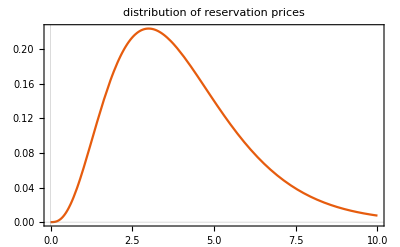

```mathematica
ℛ=GammaDistribution[4,1];
fig0=Plot[PDF[ℛ,x],{x, 0, 10},PlotRange->All,PlotTheme->"Scientific",PlotLabel->"distribution of reservation prices"]
```

```mathematica
Export["../paper/figs/w-fig-00-gamma.png",fig0]
```

../paper/figs/w-fig-00-gamma.png

The other type of distribution is about the particular style preference of an agent. Let’s call it S. We want the values of this distribution to fall in the interval [0,1]. For this, we can use the uniform distribution or a Beta distribution. The following are examples of two types of distributions. The choice of the beta distribution is smart because it contains the uniform distribution, but also it may reflect the fact that there is like a common value for the style choice with some variation.

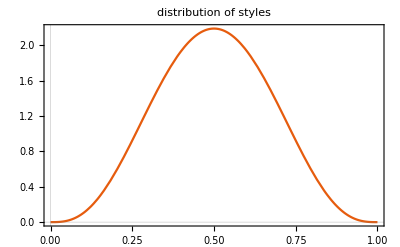

```mathematica
𝒮=BetaDistribution[4, 4];
fig1=Plot[PDF[𝒮,x],{x, 0, 1},PlotRange->All,PlotTheme->"Scientific",PlotLabel->"distribution of styles"]
```

```mathematica
Export["../paper/figs/w-fig-01-beta-44.png",fig1]
```

../paper/figs/w-fig-01-beta-44.png

We assume that the random variables R and S are independent.

The first step for the agent is to look at the price of the good. The (negative) utility of the agent from facing the good with price p and style o is the following

u(r, s, p, o)=-α·p/r-β·(s-o)^2

where r is a realization of the random variable R, s is a realization of the random variable S, p is the offered price of a good (assumed non-negative) with the style o. We can view u as the random variable

U=-α·p/R-β·(S-o)^2

In the above formula, the parameters r and s describe the consumer (the agent) and the parameters p and o describe the good. Both these parameters are controlled by a firm producing the good.

Let’s have an example

```mathematica
ℛ=GammaDistribution[4,1];
𝒮=BetaDistribution[4,4];
α=1;
β=1;
p=4;
o=9/10;
```

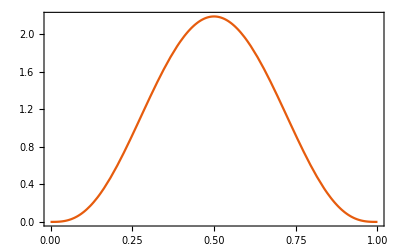

```mathematica
Plot[PDF[𝒮,z],{z,0,1},PlotTheme->"Scientific",GridLines->{{Mean[𝒮]},None}]
```

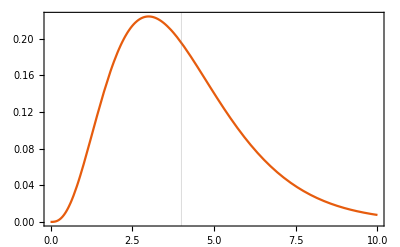

```mathematica
Plot[PDF[ℛ,z],{z,0,10},PlotTheme->"Scientific",GridLines->{{Mean[ℛ]},None}]
```

```mathematica
𝒰=TransformedDistribution[-α p/r-β (s-o)^2,{r\[Distributed]ℛ,s\[Distributed]𝒮}]
```

TransformedDistribution[-4/x1-(-9/10+x2)^2,{x1\[Distributed]GammaDistribution[4,1],x2\[Distributed]BetaDistribution[4,4]}]

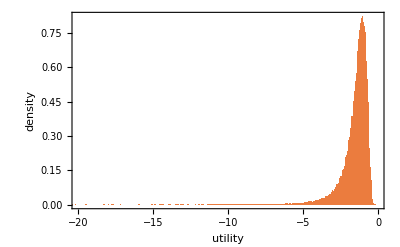

```mathematica
Histogram[RandomVariate[𝒰,10^5],"Scott","PDF",PlotTheme->"Scientific",FrameLabel->{"utility", "density"},PlotRange->{{-20,0},All},GridLines->{{.5},None}]
```

The probability that a consumer buys the good is given by the folowing formula

ℙ(buy)=(exp(u))/(1+exp(u))

and the probability of not buy is given by the following formula

ℙ(not buy)=1/(1+exp(u))=1-(exp(u))/(1+exp(u))

We can view the probability of buying as a random variable 𝒫 that reads

𝒫=ℙ(buy)=(exp(U))/(1+exp(U))=(exp(-α·p/R-β·(S-o)^2))/(1+exp(-α·p/R-β·(S-o)^2))

Note that for the smallest negative utility (that is u=0) this is equal to 1/2 and this is the highest possible value. For any lower  utility (that is higher negative utilities) this is less than 1/2. Should we multiply this by 2 to scale it to 1?

Let’s have an example for the probability of buying.

```mathematica
ℛ=GammaDistribution[4,1];
𝒮=BetaDistribution[4,4];
α=1;
β=1;
p=10;
o=1/2;
```

```mathematica
𝒫=TransformedDistribution[Exp[(-α p/r-β (s-o)^2)]/(1+Exp[(-α p/r-β (s-o)^2)]),{r\[Distributed]ℛ,s\[Distributed]𝒮}]
```

TransformedDistribution[(ⅇ^(-10/x1-(-1/2+x2)^2))/(1+ⅇ^(-10/x1-(-1/2+x2)^2)),{x1\[Distributed]GammaDistribution[4,1],x2\[Distributed]BetaDistribution[4,4]}]

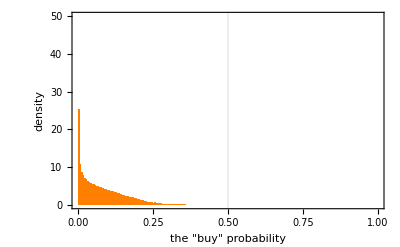

```mathematica
fig2=Histogram[RandomVariate[𝒫,10^5],"Scott","PDF",PlotTheme->"Scientific",ChartStyle->Orange,ChartBaseStyle->EdgeForm[None],FrameLabel->{"the \"buy\" probability", "density"},PlotRange->{{0,1},{0,50}},GridLines->{{.5},None}]
```

```mathematica
Export["../paper/figs/w-fig-02-p-10-0.5.png",fig2,ImageResolution->300]
```

../paper/figs/w-fig-02-p-10-0.5.png

(p=1, o = 1/2), (p=1,o=1) (p=0, o = 1/2) (p=10,o=1/2)

## A model of a firm

What is the expected profit of a single firm offering a good at price p and with the style o? We can further assume for simplicity that c(x)=c·x, and c>0. That is, that the cost function is linear. The expected profit of a firm is then the following

𝔼(profit)=𝔼(p·demand-c(demand))=𝔼(p·demand-c·demand)=𝔼(p·N·𝒫-c·N·𝒫)=𝔼((p-c)·N·𝒫)=(p-c)·N·𝔼(𝒫)

where

𝔼(𝒫)=𝔼((exp(-α·p/R-β·(S-o)^2))/(1+exp(-α·p/R-β·(S-o)^2)))=∫_0^1 ∫_0^∞ (exp(-α·p/r-β·(s-o)^2))/(1+exp(-α·p/r-β·(s-o)^2))f_R(r)f_S(s)ⅆsⅆs

Let’s have an example for the probability of buying.

```mathematica
ClearAll[expectedP]
expectedP[p_,o_,α_:1,β_:1]:=Module[
{
ℛ=GammaDistribution[4,1],
𝒮=BetaDistribution[4,4],
fr,fs,g1,x,r,s,𝒫
},
𝒫=TransformedDistribution[Exp[(-α p/r-β (s-o)^2)]/(1+Exp[(-α p/r-β (s-o)^2)]),{r\[Distributed]ℛ,s\[Distributed]𝒮}];
fr=Simplify[PDF[ℛ,r],Assumptions->r>0];
fs=Simplify[PDF[𝒮,s],Assumptions->0<s<1];
g1=fs fr Exp[-α p/r-β (s-o)^2]/(1+Exp[-α p/r-β (s-o)^2])//FullSimplify;
Quiet@NIntegrate[g1,{r,0,Infinity},{s,0,1}]
]
```

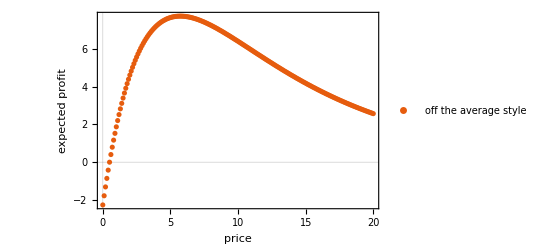

```mathematica
(* in the example the marginal cost is 1/2, there are 10 consumers and style is off the average taste *)
expectedProfit1=ParallelTable[{tp,(tp-1/2)10expectedP[tp,1/10]},{tp,0,20,0.1}];
fig1=ListPlot[Legended[expectedProfit1,"off the average style"],PlotTheme->"Scientific",FrameLabel->{"price", "expected profit"}]
```

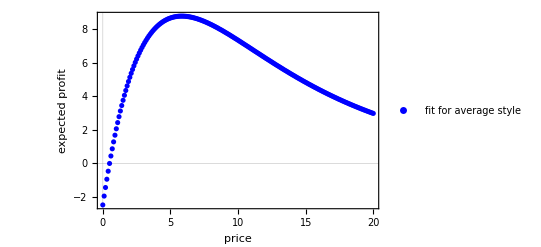

```mathematica
(* in the example the marginal cost is 1/2, there are 10 consumers and style is equal to the average taste *)
expectedProfit2=ParallelTable[{tp,(tp-1/2)10expectedP[tp,1/2]},{tp,0,20,0.1}];
fig2=ListPlot[Legended[expectedProfit2,"fit for average style"],PlotTheme->"Scientific",FrameLabel->{"price", "expected profit"},PlotStyle->Directive[Blue]]
```

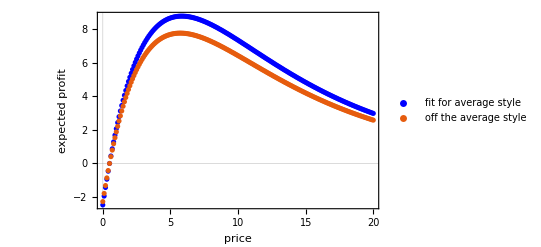

```mathematica
figOut=Show[{fig2,fig1}]
```

```mathematica
Export["../paper/figs/w-profits.png",figOut,ImageResolution->300]
```

../paper/figs/w-profits.png

## Algorithm for a firm

1. Create a population of agents.
2. Decide on the initial value for price and taste for the good.
3. Agents make their decisions.
4. The firm observes demand and can calculate the profit.
5. The firm uses the algorithm to adjust either price or the taste of the good.

## Init

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/michael/Documents/git_projects/mgr/bojarin_bogdan/MasterThesis75184SGH/wolfram